```mathematica
DifferentialD[Cos[Log[x]]]
```

ⅆCos[Log[x]]

```mathematica
f[x_] = Cos[Log[x]]
```

Cos[Log[x]]

```mathematica
f'[x]
f''[x]
```

-Sin[Log[x]]/x

-Cos[Log[x]]/x^2+Sin[Log[x]]/x^2

```mathematica
g[x_] = Sin[Log[x]]
x^2*g''[x] + x*g'[x] + g[x]
```

Sin[Log[x]]

Cos[Log[x]]+Sin[Log[x]]+x^2 (-Cos[Log[x]]/x^2-Sin[Log[x]]/x^2)

```mathematica
Simplify[%]
```

0

```mathematica
DSolve[{y'[x]==xy[x],y[0]==2},y[x],x]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument {True,True}.

DSolve[{True,True},y[x],x]

```mathematica
DSolve[y'[z]==zy[z],y[z],z]
```

DSolve::deqn: Equation or list of equations expected instead of True in the first argument True.

DSolve[True,y[z],z]

```mathematica
DSolve[y'[x]==y[x] + a Sin[x],y[x],x]
```

{{y[x]→-a Sin[x]+xy[x]}}

```mathematica
Clear[Global,"*"]
```

Clear::wrsym: Symbol a is Protected.

Clear::wrsym: Symbol b is Protected.

Clear::wrsym: Symbol c is Protected.

General::stop: Further output of Clear::wrsym will be suppressed during this calculation.

Clear::spsym: Special symbol $ActivationGroupID cannot be cleared.

Clear::spsym: Special symbol $ActivationKey cannot be cleared.

Clear::spsym: Special symbol $ActivationUserRegistered cannot be cleared.

General::stop: Further output of Clear::spsym will be suppressed during this calculation.

```mathematica
Clear["Global`*"]
```

```mathematica
DSolve[y'[x]==y[x] + a Sin[x],y[x],x]
```

{{y[x]→ⅇ^x C[1]-1/2 a (Cos[x]+Sin[x])}}

```mathematica
PacletInstall@"path/to/downloaded/CellsToTeX-0.2.2.paclet"
```

$Failed

```mathematica
PacletInstall@"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"
```

$Failed

```mathematica
PacletInstall"http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet"
```

http://github.com/jkuczm/MathematicaCellsToTeX/releases/download/v0.2.2/CellsToTeX-0.2.2.paclet PacletInstall

```mathematica
Import["https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"]
```

$Failed

```mathematica
<<https://paclets.github.io/PacletServer/Install.wl
PublicPacletInstall["CellsToTeX"]
```

Failure[…]

```mathematica
Import@"https://raw.githubusercontent.com/jkuczm/MathematicaCellsToTeX/master/NoInstall.m"
```

$Failed

{{y[x]→1/4 ⅇ^x (-1+2 x)+ⅇ^x C[1]+ⅇ^-x C[2]}}

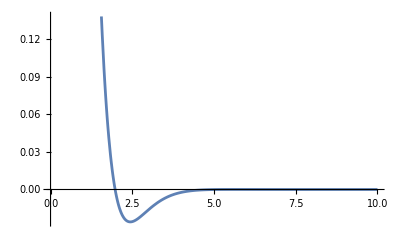
$DisplayFunction[-Graphics-]

```mathematica
y
```

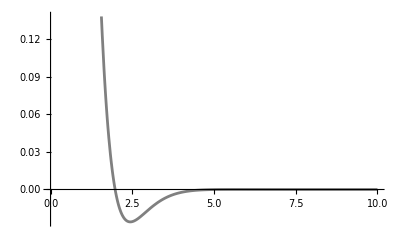
$DisplayFunction[-Graphics-]

```mathematica
Plot[Exp[-2x]*(3Sin[x] + 7Cos[x]),{x,0,10},PlotStyle->Gray]
```

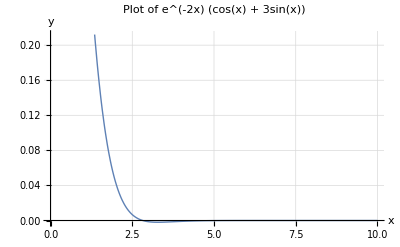
$DisplayFunction[-Graphics-]

```mathematica
Plot[Exp[-2 x] (Cos[x]+3 Sin[x]),{x,0,10},PlotStyle->Thick,AxesLabel->{"x","y"},PlotLabel->"Plot of e^(-2x) (cos(x) + 3sin(x))",GridLines->Automatic]
```

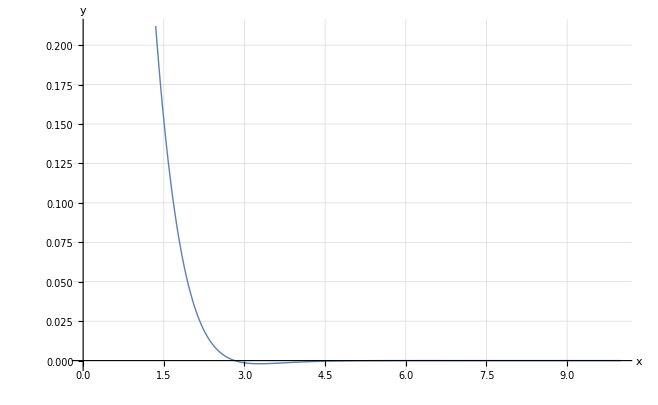

```mathematica
$DisplayFunction=Identity;
Plot[Exp[-2 x] (Cos[x]+3 Sin[x]),{x,0,10},PlotStyle->Thick,AxesLabel->{"x","y"},GridLines->Automatic]
```

```mathematica
Clear[x,y]
```

```mathematica
DSolve[y'[x]^2 +y[x] == 2,y,x]
```

{{y→Function[{x},1/4 (8-x^2-2 x C[1]-C[1]^2)]},{y→Function[{x},1/4 (8-x^2+2 x C[1]-C[1]^2)]}}

```mathematica
Simplify[%]
```

{{y→Function[{x},1/4 (8-x^2-2 x C[1]-C[1]^2)]},{y→Function[{x},1/4 (8-x^2+2 x C[1]-C[1]^2)]}}

```mathematica
DSolve[y''[x]*y'''[x] == 0,y,x]
```

{{y→Function[{x},C[1]+x C[2]]},{y→Function[{x},C[1]+x C[2]+x^2 C[3]]}}

```mathematica
DSolve[y'[x]-y[x]^2 == 1,y,x]
```

{{y→Function[{x},Tan[x+C[1]]]}}

```mathematica
DSolve[y''''[x]==x,y,x]
```

{{y→Function[{x},x^5/120+C[1]+x C[2]+x^2 C[3]+x^3 C[4]]}}

```mathematica
DSolve[y''''[x]-y[x] == x^3,y,x]
```

{{y→Function[{x},-x^3+ⅇ^x C[1]+ⅇ^-x C[3]+C[2] Cos[x]+C[4] Sin[x]]}}